```mathematica
Clear["Global`*"]
```

# Gandon 2002

```mathematica
WH[1,t_]:=pP[t](1-V) +(1-pP[t])S +(1-pP[t])(1-S)(1-V)
WH[2,t_]:=(1-pP[t])(1-V)+pP[t]S +pP[t](1-S)(1-V) 
WP[1,t_]:=pH[t]+(1-pH[t])(1-S)
WP[2,t_]:=(1-pH[t])+pH[t](1-S)
```

```mathematica
pH1[t_]:=(pH[t] WH[1,t])/(pH[t]WH[1,t]+(1-pH[t])WH[2,t])
pP1[t_]:=(pP[t] WP[1,t])/(pP[t]WP[1,t]+(1-pP[t])WP[2,t])
```

```mathematica
pH2[t_]:=pH1[t](1-mH )+mH/2
pP2[t_]:=pP1[t](1-mP)+mP/2
```

x2[t]=pH2[t]-1/2
y2[t]=pP2[t]-1/2

```mathematica
x2[t_]:=FullSimplify[pH2[t]-1/2/.{pH[t]->1/2+x[t],pP[t]->1/2+y[t]}]
```

```mathematica
y2[t_]:=FullSimplify[pP2[t]-1/2/.{pH[t]->1/2+x[t],pP[t]->1/2+y[t]}]
```

```mathematica
Δx[t_]:=x2[t]-x[t]
```

```mathematica
Δx[t]
```

-x[t]+((-1+mH) ((2+(-2+S) V) x[t]-S V y[t]))/(-2-(-2+S) V+4 S V x[t] y[t])

### Equilibria

```mathematica
equi=Solve[{x2[t]==x[t],y2[t]==y[t]},{x[t],y[t]}];
```

```mathematica
temp={x[t],y[t]}/.equi[[4]]/.{mH->ϵ μH,mP->ϵ μP};
Simplify[Series[temp[[1]],{ϵ,0,1}],Assumptions->{S>0,V>0,μH>0,ϵ>0}]
Simplify[Series[temp[[2]],{ϵ,0,1}],Assumptions->{S>0,V>0,μH>0,ϵ>0}]
```

-1/2+(μH (S V+Abs[2+(-2+S) V]) ϵ)/(4 S V)+O[ϵ]^2

Piecewise[{{-1/2+(μP ϵ)/(2 S)+O[ϵ]^2, (-2+S) V<-2}, {1/2-(((-1+S) μP) ϵ)/(2 S)+O[ϵ]^2, True}}]

### Stability

```mathematica
JMtrx={{D[x2[t],x[t]],D[x2[t],y[t]]},{D[y2[t],x[t]],D[y2[t],y[t]]}};
```

```mathematica
JMtrx1=JMtrx/.equi[[1]]//Simplify
```

{{1-mH,((-1+mH) S V)/(2+(-2+S) V)},{((-1+mP) S)/(-2+S),1-mP}}

```mathematica
λList=JMtrx1//Eigenvalues//FullSimplify
```

{-(4 (-2+mH+mP) (-1+V)+(-2+mH+mP) S^2 V-2 (-2+mH+mP) S (-1+2 V)+√(-2+S) √(2+(-2+S) V) √(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V))/(2 (-2+S) (2+(-2+S) V)),(-4 (-2+mH+mP) (-1+V)-(-2+mH+mP) S^2 V+2 (-2+mH+mP) S (-1+2 V)+√(-2+S) √(2+(-2+S) V) √(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V))/(2 (-2+S) (2+(-2+S) V))}

```mathematica
Simplify[λList[[1]],Assumptions->{mH>0,mP>0,1>S>0,0<V<1}]
```

-(4 (-2+mH+mP) (-1+V)+(-2+mH+mP) S^2 V-2 (-2+mH+mP) S (-1+2 V)+√((-2+S) (2+(-2+S) V)) √(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V))/(2 (-2+S) (2+(-2+S) V))

```mathematica
arg=(-2+S) (2+(-2+S) V)(2 (mH-mP)^2 (-2+S)+(4 (mH-mP)^2-4 (mH-mP)^2 S+(-2+mH+mP)^2 S^2) V);
```

```mathematica
re=Re[λList[[2]]/.{S->1,V->1,mH->0.15,mP->0.15}]
im=Im[λList[[2]]/.{S->1,V->1,mH->0.15,mP->0.15}]
```

0.85

-0.85

```mathematica
Sqrt[re^2+im^2]
```

1.20208

```mathematica
Reduce[{λList[[2]]>1,0<mH,0<mP,0<S<1,0<V<1}]
```

False

## Discrete-Time With a’s

```mathematica
WH[1,t_]:=pP[t](1-V) +(1-pP[t])S +(1-pP[t])(1-S)(1-V)
WH[2,t_]:=(1-pP[t])(1-V)+pP[t]S +pP[t](1-S)(1-V) 
WP[1,t_]:=pH[t] (1+a)+(1-pH[t])(1-S)(1+a)+(1-pH[t])S
WP[2,t_]:=(1-pH[t])(1+a)+pH[t](1-S)(1+a)+pH[t]S
```

```mathematica
WH[1,t]//Simplify
```

1+(-1+S) V-S V pP[t]

```mathematica
1-V+SV(1-pP)
```

```mathematica
Collect[Simplify[X pP[t](1-V)+Y(1-pP[t])(1-V)+(1-X)pP[t]+(1-Y)(1-pP[t])],{X,Y}]
```

1-V X pP[t]+Y (-V+V pP[t])

```mathematica
pH1[t_]:=(pH[t] WH[1,t])/(pH[t]WH[1,t]+(1-pH[t])WH[2,t])
pP1[t_]:=(pP[t] WP[1,t])/(pP[t]WP[1,t]+(1-pP[t])WP[2,t])
```

```mathematica
pH2[t_]:=pH1[t](1-mH )+mH/2
pP2[t_]:=pP1[t](1-mP)+mP/2
```

x2[t]=pH2[t]-1/2
y2[t]=pP2[t]-1/2

```mathematica
x2[t_]:=FullSimplify[pH2[t]-1/2/.{pH[t]->1/2+x[t],pP[t]->1/2+y[t]}]
```

```mathematica
y2[t_]:=FullSimplify[pP2[t]-1/2/.{pH[t]->1/2+x[t],pP[t]->1/2+y[t]}]
```

```mathematica
y2[t]
```

-((-1+mP) (a S x[t]+(2-a (-2+S)) y[t]))/(2-a (-2+S)+4 a S x[t] y[t])

### Equilibria

```mathematica
equi=Solve[{x2[t]==x[t],y2[t]==y[t]},{x[t],y[t]}];
```

```mathematica
equi[[1]]
```

{x[t]→0,y[t]→0}

```mathematica
temp={x[t],y[t]}/.equi[[4]]/.{mH->ϵ μH,mP->ϵ μP};
Simplify[Series[temp[[1]],{ϵ,0,1}],Assumptions->{S>0,V>0,μH>0,ϵ>0,a>0}]
Simplify[Series[temp[[2]],{ϵ,0,1}],Assumptions->{S>0,V>0,μH>0,ϵ>0,a>0}]
```

-1/2+(μH (S V+Abs[2+(-2+S) V]) ϵ)/(4 S V)+O[ϵ]^2

Abs[2+(-2+S) V]/(4+2 (-2+S) V)+1/4 μP (-1+2/S+2/(a S)-Abs[2+(-2+S) V]/(2+(-2+S) V)) ϵ+O[ϵ]^2

### Stability

```mathematica
JMtrx={{D[x2[t],x[t]],D[x2[t],y[t]]},{D[y2[t],x[t]],D[y2[t],y[t]]}};
```

```mathematica
JMtrx1=JMtrx/.equi[[1]]//Simplify
```

{{1-mH,((-1+mH) S V)/(2+(-2+S) V)},{(a (-1+mP) S)/(-2+a (-2+S)),1-mP}}

```mathematica
λList=JMtrx1//Eigenvalues//FullSimplify
```

{1/2 (2-mH-mP-(√((-2+a (-2+S)) (2 (mH-mP)^2 (-2+a (-2+S))+(4 (1+a) (mH-mP)^2-2 (1+2 a) (mH-mP)^2 S+a (-2+mH+mP)^2 S^2) V)))/((-2+a (-2+S)) √(2+(-2+S) V))),1/2 (2-mH-mP+(√((-2+a (-2+S)) (2 (mH-mP)^2 (-2+a (-2+S))+(4 (1+a) (mH-mP)^2-2 (1+2 a) (mH-mP)^2 S+a (-2+mH+mP)^2 S^2) V)))/((-2+a (-2+S)) √(2+(-2+S) V)))}

```mathematica
re=Re[λList[[1]]/.{S->0.5,V->0.8,mH->0.01,mP->0.01,a->0.01}]
im=Im[λList[[1]]/.{S->0.5,V->0.8,mH->0.01,mP->0.01,a->0.01}]
```

0.99

0.0348713

```mathematica
Sqrt[re^2+im^2]
```

0.990614

## Individual-Based Simulations

```mathematica
parsN={X->0.5,V->0.2,a->0.1,mH->0.01,mP->0.01,κH->100,κP->100,tMax->500};
pars1={X->0.8,V->0.2,a->0.1,mH->0.01,mP->0.01,κH->100,κP->100,tMax->500};
pars2={X->0.6,V->0.2,a->0.1,mH->0.01,mP->0.01,κH->100,κP->100,tMax->500};
```

Absolute Fitnesses

```mathematica
WH[1,pVec_]:=1-V(X pVec[[2]]+Y(1-pVec[[2]]))/.Y->(1-X)
WH[2,pVec_]:=1-V(Y pVec[[2]]+X(1-pVec[[2]]))/.Y->(1-X) 
WP[1,pVec_]:=1+a(X pVec[[1]]+Y(1-pVec[[1]]))/.Y->(1-X)
WP[2,pVec_]:=1+a(Y pVec[[1]]+X(1-pVec[[1]]))/.Y->(1-X)
```

Relative fitnesses

```mathematica
wH[pVec_]:=WH[1,pVec]/(pVec[[1]] WH[1,pVec]+(1-pVec[[1]])WH[2,pVec]) 
wP[pVec_]:=WP[1,pVec]/(pVec[[2]] WP[1,pVec]+(1-pVec[[2]])WP[2,pVec])
```

```mathematica
WH[1,{0.5,0.5}]/.pars1
```

0.9

```mathematica
WH[2,{0.5,0.5}]/.pars1
```

0.9

```mathematica
wH[{0.5,0.5}]/.pars1
```

0.967742

```mathematica
Clear[Sim]
Sim[pars_,intS_]:=Sim[pars,intS]=Block[{out,g,nH,nP,nM1,nM2},out={{1/2,1/2}}//N;
For[g=1,g≤(tMax/.pars),g++,
(*Selection*)
nH=RandomVariate[BinomialDistribution[(κH/.pars),wH[out[[-1]]]out[[-1,1]]/.pars]];
nP=RandomVariate[BinomialDistribution[(κP/.pars),wP[out[[-1]]]out[[-1,2]]/.pars]];
(*Migration*)
nM1=RandomVariate[BinomialDistribution[nH,mH/.pars]];(*Number of type 1 host migrants*)
nM2=RandomVariate[BinomialDistribution[(κH/.pars)-nH,mH/.pars]];(*Number of type 2 host migrants*)
nH=nH-nM1+RandomVariate[BinomialDistribution[nM1,0.5]]+RandomVariate[BinomialDistribution[nM2,0.5]];(*Number of type 1 hosts after migration*)
nM1=RandomVariate[BinomialDistribution[nP,mP/.pars]];(*Number of type 1 host migrants*)
nM2=RandomVariate[BinomialDistribution[(κP/.pars)-nP,mP/.pars]];(*Number of type 2 host migrants*)
nP=nP-nM1+RandomVariate[BinomialDistribution[nM1,0.5]]+RandomVariate[BinomialDistribution[nM2,0.5]];(*Number of type 1 hosts after migration*)
AppendTo[out,{nH/κH,nP/κP}/.pars//N]
];
out
]
```

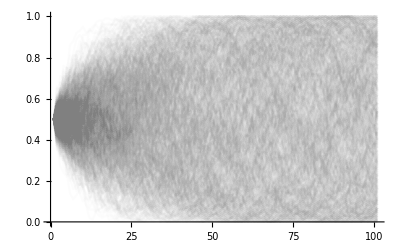

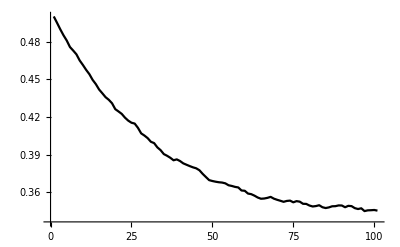

```mathematica
ListLinePlot[Table[Sim[pars1,j][[;;,1]],{j,1,1000}],PlotStyle->Directive[Gray,Opacity[0.02]]]
```

```mathematica
leg=LineLegend[{Black,Blue,Red},{"Neutral","Weak Coev. X=0.6","Strong Coev. X=0.8"}];
```

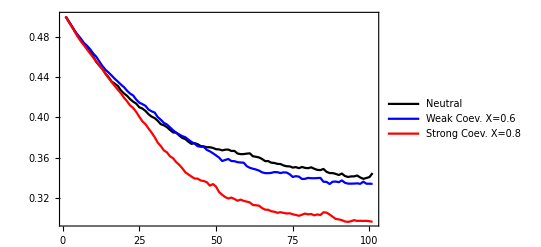

```mathematica
Show[ListLinePlot[Mean[Table[2 Sim[parsN,j][[;;,1]](1-Sim[parsN,j][[;;,1]]),{j,1,1000}]],PlotStyle->Black],ListLinePlot[Mean[Table[2 Sim[pars2,j][[;;,1]](1-Sim[pars2,j][[;;,1]]),{j,1,1000}]],PlotStyle->Blue],ListLinePlot[Mean[Table[2 Sim[pars1,j][[;;,1]](1-Sim[pars1,j][[;;,1]]),{j,1,1000}]],PlotStyle->Red],PlotRange->All,Frame->True,Axes->False,Epilog->Inset[leg,Scaled[{0.8,0.8}]],FrameTicksStyle->Directive[Black,16],Background->White]
```

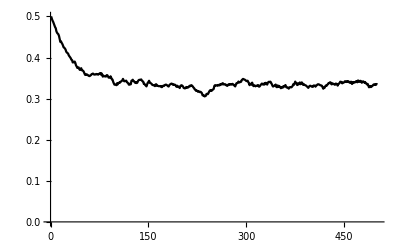

```mathematica
ListLinePlot[Mean[Table[2 Sim[parsN,j][[;;,1]](1-Sim[parsN,j][[;;,1]]),{j,1,250}]],PlotRange-> {0,0.5},PlotStyle->Black]
```

## Continuous-Time limit

```mathematica
WH[1,t_]:=1-V Δt+S V Δt (1-pP[t])
WH[2,t_]:=1-V Δt+S V Δt pP[t]
WP[1,t_]:=1+a Δt-a Δt S(1-pH[t])
WP[2,t_]:=1+a Δt-a Δt S pH[t]
```

```mathematica
pH1[t_]:=(pH[t] WH[1,t])/(pH[t]WH[1,t]+(1-pH[t])WH[2,t])
pP1[t_]:=(pP[t] WP[1,t])/(pP[t]WP[1,t]+(1-pP[t])WP[2,t])
```

```mathematica
pH2[t_]:=pH1[t](1-Δt mH )+(Δt mH)/2
pP2[t_]:=pP1[t](1-Δt mP)+(Δt mP)/2
```

```mathematica
Limit[Factor[pH2[t]-pH[t]]/Δt,Δt->0]/.{pH[t]->x[t]+1/2,pP[t]->y[t]+1/2}//Factor
```

1/2 (-2 mH x[t]-S V y[t]+4 S V x[t]^2 y[t])

```mathematica
Limit[Factor[pP2[t]-pP[t]]/Δt,Δt->0]/.{pH[t]->x[t]+1/2,pP[t]->y[t]+1/2}//Factor
```

1/2 (a S x[t]-2 mP y[t]-4 a S x[t] y[t]^2)

```mathematica
f1[t_]:=1/2 (-2 mH x[t]-S V y[t]+4 S V x[t]^2 y[t])
f2[t_]:=1/2 (a S x[t]-2 mP y[t]-4 a S x[t] y[t]^2)
```

```mathematica
equi=Solve[{f1[t]==0,f2[t]==0},{x[t],y[t]}];
```

```mathematica
JMtrx={{D[f1[t],x[t]],D[f1[t],y[t]]},{D[f2[t],x[t]],D[f2[t],y[t]]}};
```

```mathematica
λList=Simplify[Eigenvalues[JMtrx/.equi[[1]]],Assumptions->{mH>0,mP>0,S>0,V>0}]
```

{1/2 (-mH-mP-√(mH^2-2 mH mP+mP^2-a S^2 V)),1/2 (-mH-mP+√(mH^2-2 mH mP+mP^2-a S^2 V))}

```mathematica
Reduce[{mH^2-2 mH mP+mP^2-a S^2 V>0,mH>0,mP>0,S>0,V>0,a>0}]//Simplify
```

0<a<(mH-mP)^2/(S^2 V)&&(0<mH<mP||mH>mP)&&mP>0&&S>0&&V>0

```mathematica
λList[[1]]
```

1/2 (-mH-mP-√(mH^2-2 mH mP+mP^2-a S^2 V))

```mathematica
Reduce[{λList[[1]]>0,λList[[2]]>0,mH>0,mP>0,S>0,V>0,a>0}]
```

False